```mathematica
SetDirectory[NotebookDirectory[]];
```

## Source: doi:10.1115/1.3446925

## Initial data

```mathematica
data={a->0.1,σ0->-50,σxx->-50.0,σyy->-50.0,σzz->-50.0,τxy->0.0,τxz->0.0,τyz->0.0,pw->-10.0,λ-> 555.55555555555554,G->833.33333333333337,ν->λ/(2(λ+G)),θ->0 ,re->4.0,rw->0.1};
```

## General 2D loading Cylindrical coordinates: Bradley equations:

```mathematica
σrr=(σxx+σyy)/2(1-(a/r)^2)+(1-4(a/r)^2+3(a/r)^4)((σxx-σyy)/2)Cos[2θ]+τxy (1-4(a/r)^2+3(a/r)^4)Sin[2 θ]+pw (a/r)^2-σ0;
σθθ=(σxx+σyy)/2(1+(a/r)^2)-(1+3(a/r)^4)((σxx-σyy)/2)Cos[2θ]-τxy (1+3(a/r)^4)Sin[2 θ]-pw (a/r)^2-σ0;
σžž=σzz-ν(2(σxx-σyy)(a/r)^2 Cos[2θ]+4 τxy (a/r)^2 Sin[2 θ])-σ0;
τrθ=(1+2(a/r)^2-3(a/r)^4)((σyy-σxx)/2)Sin[2θ]+τxy (1-3(a/r)^4+2(a/r)^2)Cos[2 θ];
τθz=(-τxz Sin[ θ]+τyz Cos[θ])(1+(a/r)^2);
τrz=(τxz Cos[θ]+τyz Sin[θ])(1-(a/r)^2);
σcyl={{σrr,τrθ,τrz},{τrθ,σθθ,τθz},{τrz,τθz,σžž}};
```

```mathematica
divσcyl=Div[σcyl,{r,θ,z},"Cylindrical"];
```

```mathematica
σrr//.{σxx->σyy,τxy->0}
σθθ//.{σxx->σyy,τxy->0}
σžž//.{σxx->σyy,τxy->0}
```

(a^2 pw)/r^2-σ0+(1-a^2/r^2) σyy

-(a^2 pw)/r^2-σ0+(1+a^2/r^2) σyy

-σ0+σzz

proof

```mathematica
{0,0,0}==divσcyl//Simplify
```

True

```mathematica
σrr//.data//.r->10.0
σθθ//.data//.r->10.0
σžž//.data//.r->10.0
```

0.004

-0.004

0.

## General 2D loading on Cartesian coordinates :

```mathematica
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};
ecyl1=x/(√(x^2+y^2)) e1+y/(√(x^2+y^2)) e2;
ecyl2=-y/(√(x^2+y^2)) e1+x/(√(x^2+y^2)) e2;
ecyl3=e3;
CylToCarTrule={r->√(x^2+y^2),θ-> ArcTan[y/x]};
```

```mathematica
σcart=σrr TensorProduct[ecyl1,ecyl1]+τrθ TensorProduct[ecyl1,ecyl2]+τrz TensorProduct[ecyl1,ecyl3]+τrθ TensorProduct[ecyl2,ecyl1]+σθθ TensorProduct[ecyl2,ecyl2]+τθz TensorProduct[ecyl2,ecyl3]+τrz TensorProduct[ecyl3,ecyl1]+τθz TensorProduct[ecyl3,ecyl2]+σžž TensorProduct[ecyl3,ecyl3]//.CylToCarTrule//Simplify;
divσcart=Div[σcart,{x,y,z},"Cartesian"];
```

proof

```mathematica
{0,0,0}==divσcart//Simplify
```

True

## Comparing the values

```mathematica
rθrule={r->√(x^2+y^2)//.{x->0.1,y->0.0},θ-> ArcTan[y/x]//.{x->0.1,y->0.0}};
σcart//.data//.{x->0.1,y->0.0}
σcyl//.data//.rθrule
```

{{40.,0.,0.},{0.,-40.,0.},{0.,0.,0.}}

{{40.,0.,0.},{0.,-40.,0.},{0.,0.,0.}}

## Color for plot

```mathematica
fontsizewrite=10;
fontsize=15;
gblue=RGBColor[0.0274,0.1254,0.349];
gred=RGBColor[0.549,0.0196,0.0235];
```

## Render analytical plots

```mathematica
rev=re//.data;
```

```mathematica
gsxxAnal=Plot[σcart[[1,1]]//.data//.{y->0},{x,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_x",gred,fontsizewrite],Right]];
gsyyAnal=Plot[σcart[[2,2]]//.data//.{y->0},{x,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_y",gred,fontsizewrite],Right]];
gsZZAnal=Plot[σcart[[3,3]]//.data//.{y->0},{x,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_z",gred,fontsizewrite],Right]];
```

## Render analytical plots

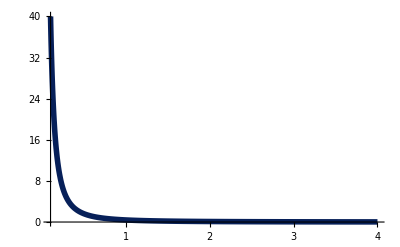

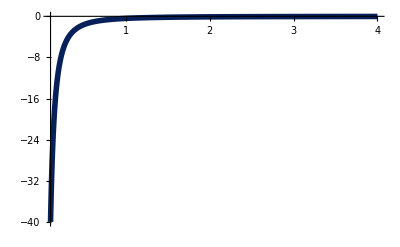

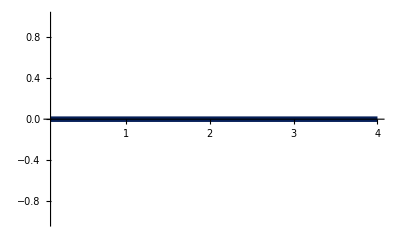

```mathematica
gsrrAnal=Plot[σcyl[[1,1]]//.data,{r,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_r",gred,fontsizewrite],Right]]
gsθθAnal=Plot[σcyl[[2,2]]//.data,{r,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_θ",gred,fontsizewrite],Right]]
gszzAnal=Plot[σcyl[[3,3]]//.data,{r,0.1,rev},PlotRange->All,PlotStyle->{gblue,Thickness[0.01]},PlotLegends->Placed[Style["Analytical σ_z",gred,fontsizewrite],Right]]
```

## Check Cartesian

```mathematica
Print["sigma x = ",σcart[[1,1]]//.data//.{y->0}//.x->10]
```

sigma x = 0.004

```mathematica
Print["sigma y = ",σcart[[2,2]]//.data//.{y->0}//.x->10]
```

sigma y = -0.004

## Check Cylindrical

```mathematica
Print["sigma r = ",σcyl[[1,1]]//.r->re//.data]
```

sigma r = 0.025

```mathematica
Print["sigma θ = ",σcyl[[2,2]]//.r->re//.data]
```

sigma θ = -0.025

```mathematica
Print["sigma z = ",σcyl[[3,3]]//.r->re//.data]
```

sigma z = 0.

## RK approximation

Getting the initial data

```mathematica
σrratRe=σcyl[[1,1]]//.r->re//.data;
σθθatRe=σcyl[[2,2]]//.r->re//.data;
σzzatRe=σcyl[[3,3]]//.r->re//.data;
uratRe=-(r σcyl[[3,3]]-r σcyl[[2,2]])/(2 G)//.r->re//.data;
y0={uratRe,σrratRe}
```

{-0.00006,0.025}

```mathematica
{σrratRe,σθθatRe,σzzatRe}
```

{0.025,-0.025,0.}

```mathematica
σθθexp=(2 G ur)/r+λ (ur/r+(r σrr-λ ur)/(r (λ+2 G)));
σzzexp=λ (ur/r+(r σrr-λ ur)/(r (λ+2 G)));
σzzexp=λ (ur/r+(r σrr-λ ur)/(r (λ+2 G))); 
σzzexp=-(λ (λ (σrr-2 σrr-σθθexp)-2 G (σrr+σθθexp)))/(2 (λ+G) (λ+2 G))//Simplify;
```

Construct f(r,σr) vector

```mathematica
fvec[r_,ur_,σrr_]:={(r σrr-λ ur)/(r λ+2 r G),(-σrr+((2 G ur)/r+λ (ur/r+(r σrr-λ ur)/(r (λ+2 G)))))/r}//.data;
```

## Geometry with Progression geometry

```mathematica
(*np=500;
r=0.99930;
xl=0.1;
xr=10.0;
L=xr-xl;
zval=xl;
ptsdata={};
AppendTo[ptsdata,xl];
For[i=1,i<np,i++,
dzn=(L/np) r^(np-i);
zval+=dzn;
AppendTo[ptsdata,zval];
];
AppendTo[ptsdata,xr];*)
(*hdata=-Table[ptsdata[[i]]/np,{i,1,np}];*)
(*hdata=-Table[Norm[ptsdata[[i]]-ptsdata[[i+1]]]/np,{i,1,np}];*)
```

```mathematica
(*ListPlot[hdata]*)
```

RK process

```mathematica
ydata={};
sdata={};
np=5000;
h=(rw-re)/np//.data
yn=y0;
rn=re//.data;
AppendTo[ydata,Flatten[{rn,yn}]];
AppendTo[sdata,Flatten[{rn,σθθatRe,σzzatRe}]];
```

-0.00078

```mathematica
For[i=1,i<np,i++,
(*h=hdata[[i]];*)
k1=h fvec[rn,yn[[1]],yn[[2]]];
k2=h fvec[rn+h/2,yn[[1]]+k1[[1]]/2,yn[[2]]+k1[[2]]/2];
k3=h fvec[rn+h/2,yn[[1]]+k2[[1]]/2,yn[[2]]+k2[[2]]/2];
k4=h fvec[rn+h,yn[[1]]+k3[[1]],yn[[2]]+k3[[2]]];
ynpone=yn+1/6(k1+2k2+2k3+k4);
rnpone=rn+h;
AppendTo[ydata,Flatten[{rnpone,ynpone}]];
AppendTo[sdata,Flatten[{rn,σθθexp,σzzexp}//.{r->rnpone,ur-> ynpone[[1]],σrr-> ynpone[[2]]}//.data]];
rn=rnpone;
yn=ynpone;
];
```

```mathematica
(*For[i=1,i<np,i++,
k1=h fvec[rn,yn[[1]],yn[[2]]];
ynpone=yn+(k1);
rnpone=rn+h;
AppendTo[ydata,Flatten[{rnpone,ynpone}]];
AppendTo[sdata,Flatten[{rn,σθθexp,σzzexp}//.{r->rnpone,ur-> ynpone[[1]],σrr-> ynpone[[2]]}//.data]];
rn=rnpone;
yn=ynpone;
];*)
```

```mathematica
grkur=ListPlot[ydata[[All,{1,2}]],PlotStyle->Red];
grkσrr=ListPlot[ydata[[All,{1,3}]],PlotStyle->Red];
grkσtt=ListPlot[sdata[[All,{1,2}]],PlotStyle->Red];
grkσzz=ListPlot[sdata[[All,{1,3}]],PlotStyle->Red];
```

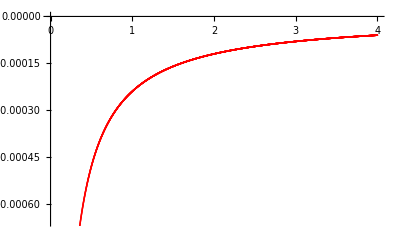
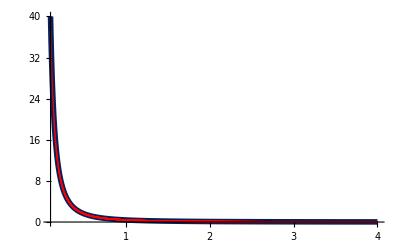
ur | σrr
-Graphics- | -Graphics-

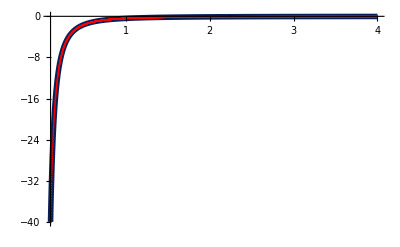
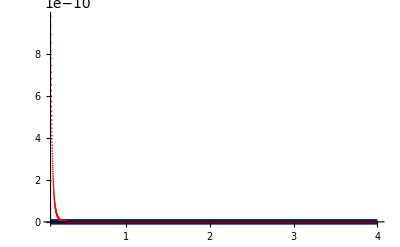
σtt | σzz
-Graphics- | -Graphics-

```mathematica
imagesize=400;
Grid[{{"ur","σrr"},{Show[{grkur},ImageSize->imagesize],Show[{gsrrAnal,grkσrr},ImageSize->imagesize]}},Frame->All]
Grid[{{"σtt","σzz"},{Show[{gsθθAnal,grkσtt},ImageSize->imagesize],Show[{gszzAnal,grkσzz},ImageSize->imagesize]}},Frame->All]
```

```mathematica
gszzAnal
```

-Graphics-